```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\蛋白质浓度测量\\Bradford.xlsx"]
```

```mathematica
data2={{0.,0.0015},{10.,0.0545},{20.,0.14850000000000002},{40.,0.28200000000000003},{60.,0.3945},{80.,0.5365},{100.,0.6365000000000001}}
```

{{0.,0.0015},{10.,0.0545},{20.,0.1485},{40.,0.282},{60.,0.3945},{80.,0.5365},{100.,0.6365}}

```mathematica
lm2=LinearModelFit[data2,x,x]
```

FittedModel[0.0073814+0.00645913 x]

```mathematica
Normal[lm2]
```

0.0073814+0.00645913 x

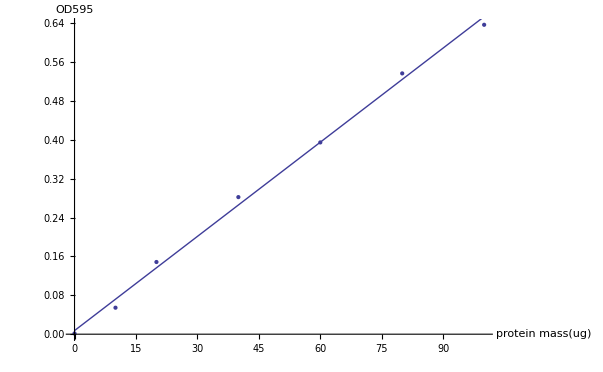

```mathematica
Show[ListPlot[data2],Plot[lm2[x],{x,0,100}],AxesLabel-> {"protein mass(ug)","OD595"}]
```

```mathematica
lm2["RSquared"]
```

0.996626